```mathematica
(*початкові дані згідно варіанту 3*)
f[x1_,x2_]=x1^2+x2^2-8x1-10x2;
g[x1_,x2_]={-2+2 x1^2+x2^2,-x1 ,-x2};(* ≤0 *)
h[x1_,x2_]=x1+x2-1.5; (* ==0 *)
X0={0.1,0.1};
```

```mathematica
(*функція, яка повертатиме значення градієнта в точці*)
Gr[f_,X0_]:=Grad[f[x1,x2],{x1,x2}]/.Thread[{x1,x2}->X0]
(*функція, яка повертає гессіан функції в точці*)
H[f_,X0_]:=({{D[f[x1,x2],{x1,2}], D[f[x1,x2],x1,x2]}, {D[f[x1,x2],x2,x1], D[f[x1,x2],{x2,2}]}})/.Thread[{x1,x2}->X0];
(* градієнтний метод найшлвидшого спуску *)
GradMethod[F_,X0_,ϵ_]:=(
XRes={X0}; 
i=1; 

While[Norm[Gr[F,XRes[[-1]]]]>ϵ,{
If[Length[XRes]≥1000,Break[]]; 
Clear[α];
temp=XRes[[-1]]-α  (Gr[F,XRes[[-1]]]);
FF[α_]=F[temp[[1]],temp[[2]]];

α=Minimize[{FF[α],α>0},α][[2,1,2]];
AppendTo[XRes,XRes[[-1]]-α*Gr[F,XRes[[-1]]]]; (* обчислення нового наближення *)
}];
Return[XRes[[-1]]]
)

(* Метод модифікована функція Лагранжа *)
ModifiedLagrangianFunction[f_,h_,g_,X0_]:=(
t1=Now;
λ0=0.;
c0=0.1;
μ0=Table[0,{i,1,Length[g[x1,x2]]}];
β=10.;
Γ=0.25;
X={X0};
k=0;
res={{"k","X","f[X]","λ","c","μ"},{k,X[[-1]],f[X[[-1,1]],X[[-1,2]]],λ0,c0,μ0}};
L[x1_,x2_,λ_,μk_,c_]=f[x1,x2]+λ h[x1,x2]+1/2 c (h[x1,x2])^2+1/(2c)Sum[Max[0,μk[[i]]+c g[x1,x2][[i]]]^2-μk[[i]]^2,{i,1,Length[g[x1,x2]]}];
l[x1_,x2_]=L[x1,x2,λ0,μ0,c0];
AppendTo[X,GradMethod[l,X[[-1]],ϵ]];
(*AppendTo[X,NMinimize[l[x1,x2],{x1,x2}][[2,;;,2]]];*)
λ1=λ0+c0 h[X[[-1,1]],X[[-1,2]]];
μ1=μ0+c0  Table[Max[g[X[[-1,1]],X[[-1,2]]][[i]],-μ0[[i]]/c0],{i,1,Length[g[x1,x2]]}];
If[Abs[h[X[[-1,1]],X[[-1,2]]]]>Γ Abs[h[X[[-2,1]],X[[-2,2]]]],c1=β c0,c1=c0];
k++;
AppendTo[res,{k,X[[-1]],f[X[[-1,1]],X[[-1,2]]],λ1,c1,μ1}];
While[Norm[X[[-1]]-X[[-2]]]>ϵ,{
If[k≥50,Break[]];
l[x1_,x2_]=L[x1,x2,λ1,μ1,c1];
AppendTo[X,GradMethod[l,X[[-1]],ϵ]];

λ2=λ1+c1 h[X[[-1,1]],X[[-1,2]]];
μ2=μ1+c1 Table[Max[g[X[[-1,1]],X[[-1,2]]][[i]],-μ1[[i]]/c1],{i,1,Length[g[x1,x2]]}];
If[Abs[h[X[[-1,1]],X[[-1,2]]]]>Γ Abs[h[X[[-2,1]],X[[-2,2]]]],c2=β c1,c2=c1];
(*c2=0.1 8^(k+1);*)
k++;
AppendTo[res,{k,X[[-1]],f[X[[-1,1]],X[[-1,2]]],λ2,c2,μ2}];
λ1=λ2;
c1=c2;
μ1=μ2;

}];
t2=Now;

point=NMinimize[{f[x1,x2],g[x1,x2][[1]]≤0,g[x1,x2][[2]]≤0,g[x1,x2][[3]]≤0,h[x1,x2]==0},{x1,x2}][[2,;;,2]];
Print["Таблиця результатів: \n",Grid[res]];
Print["Час роботи методу: ",t=t2-t1, "\nНев'язка: ",Norm[point-X[[-1]] ],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]],"\nОтримане значення: ",X[[-1]],"\nЗначення функції: ",f[X[[-1,1]],X[[-1,2]]]];

Return[X[[-1]]]
)
PenaltyMethod[f_,h_,g_,α_,c_,X0_]:=(
t1=Now;
Α={α};
X={X0};
Φ[x1_,x2_,ak_]=1/ak(Sum[Max[0,g[x1,x2][[i]]]^2,{i,1,Length[g[x1,x2]]}]+(h[x1,x2])^2);

F[x1_,x2_,ak_]=f[x1,x2]+Φ[x1,x2,ak];
k=0;
res={{"k","X","f[X]","a"},{k,X[[-1]],f[X[[-1,1]],X[[-1,2]]],Α[[-1]]}};
While[Abs[Φ[X[[-1,1]],X[[-1,2]],Α[[-1]]]]≥ϵ,{
If[k≥10,Break[]];
k++;
Ftemp[x1_,x2_]=F[x1,x2,Α[[-1]]];
AppendTo[X,GradMethod[Ftemp,X[[-1]],ϵ]];
(*AppendTo[X,NMinimize[Ftemp[x1,x2],{x1,x2}][[2,;;,2]]];*)
AppendTo[Α,Α[[-1]]/c];
AppendTo[res,{k,X[[-1]],f[X[[-1,1]],X[[-1,2]]],Α[[-1]]}];
}];

t2=Now;

point=NMinimize[{f[x1,x2],g[x1,x2][[1]]≤0,g[x1,x2][[2]]≤0,g[x1,x2][[3]]≤0,h[x1,x2]==0},{x1,x2}][[2,;;,2]];
Print["Таблиця результатів: \n",Grid[res]];
Print["Час роботи методу: ",t=t2-t1, "\nНев'язка: ",Norm[point-X[[-1]] ],"\nПохибка: ",Abs[f[point[[1]],point[[2]]]-f[X[[-1,1]],X[[-1,2]]]],"\nОтримане значення: ",X[[-1]],"\nЗначення функції: ",f[X[[-1,1]],X[[-1,2]]]];
Return[X[[-1]]]
)
```

```mathematica
NMinimize[{f[x1,x2],g[x1,x2][[1]]≤0,g[x1,x2][[2]]≤0,g[x1,x2][[3]]≤0,h[x1,x2]==0},{x1,x2}]
pointt=%[[2,;;,2]];
Show[Plot3D[f[x,y],{x,-10,10},{y,-10,10},PlotStyle->{Opacity[0.8]},MeshFunctions->{#3&},Mesh->50]]
```

{-12.875,{x1→0.25,x2→1.25}}

-Graphics3D-

Таблиця результатів: 
k | X | f[X] | λ | c | μ
0 | {0.1,0.1} | -1.78 | 0. | 0.1 | {0,0,0}
1 | {1.40996,2.60089} | -28.536 | 0.251085 | 1. | {0.874061,0.,0.}
2 | {0.693409,1.48741} | -17.7282 | 0.931905 | 10. | {2.04809,0.,0.}
3 | {0.516817,1.20278} | -14.4485 | 3.12784 | 100. | {1.8568,0.,0.}
4 | {0.271782,1.27151} | -13.1987 | 7.45671 | 100. | {0.,0.,0.}
5 | {0.250351,1.25008} | -12.8782 | 7.49957 | 100. | {0.,0.,0.}
6 | {0.250138,1.24987} | -12.875 | 7.49999 | 100. | {0.,0.,0.}

Час роботи методу: 1.5893 s
Нев'язка: 0.000191479
Похибка: 0.0000317005
Отримане значення: {0.250138,1.24987}
Значення функції: -12.875

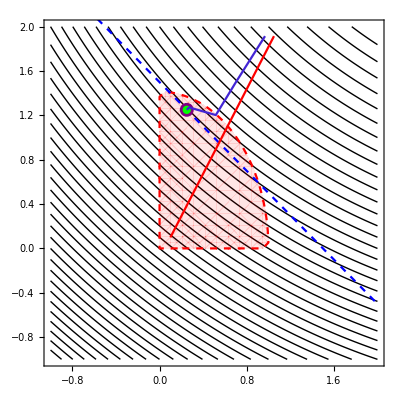

```mathematica
point1=ModifiedLagrangianFunction[f,h,g,X0];
Show[
ContourPlot[f[x1,x2],{x1,-1,2},{x2,-1,2},ContourShading->None,Contours->{Automatic,50}],RegionPlot[g[x1,x2][[1]]≤0&&g[x1,x2][[2]]≤0&&g[x1,x2][[3]]≤0,{x1,-r,r},{x2,-r,r},PlotStyle->{Red,Opacity[0.1]},BoundaryStyle->{Dashed,Red}],Plot[Reduce[h[x1,x2]==0,x2][[2]]==0,{x1,-r,r},PlotStyle->{Blue,Dashed}],
Graphics[{Purple,PointSize[0.025],Point[pointt],Green,PointSize[0.015],Point[point1]}],

ListLinePlot[X,ColorFunction->Function[{x,y},Hue[y]]]
]
```

Таблиця результатів: 
k | X | f[X] | a
0 | {0.1,0.1} | -1.78 | 1.
1 | {0.671287,1.45142} | -17.3272 | 0.25
2 | {0.558925,1.26998} | -15.246 | 0.0625
3 | {0.421515,1.28614} | -14.4017 | 0.015625
4 | {0.279188,1.27895} | -13.3094 | 0.00390625
5 | {0.257428,1.25719} | -12.9845 | 0.000976563
6 | {0.251948,1.25171} | -12.9024 | 0.000244141
7 | {0.250576,1.25034} | -12.8819 | 0.0000610352
8 | {0.250233,1.25} | -12.8767 | 0.0000152588
9 | {0.250147,1.24991} | -12.8754 | 3.8147×10^-6

Час роботи методу: 3.1525 s
Нев'язка: 0.000171838
Похибка: 0.000429121
Отримане значення: {0.250147,1.24991}
Значення функції: -12.8754

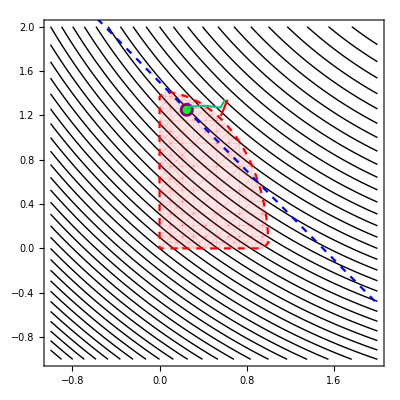

```mathematica
point2=PenaltyMethod[f,h,g,1.,4.,X0];
Show[
ContourPlot[f[x1,x2],{x1,-1,2},{x2,-1,2},ContourShading->None,Contours->{Automatic,50}],

RegionPlot[g[x1,x2][[1]]≤0&&g[x1,x2][[2]]≤0&&g[x1,x2][[3]]≤0,{x1,-r,r},{x2,-r,r},PlotStyle->{Red,Opacity[0.1]},BoundaryStyle->{Dashed,Red}],

Plot[Reduce[h[x1,x2]==0,x2][[2]]==0,{x1,-r,r},PlotStyle->{Blue,Dashed}],

Graphics[{Purple,PointSize[0.025],Point[pointt],Green,PointSize[0.015],Point[point2]}],

ListLinePlot[X,ColorFunction->Function[{x,y},Hue[y]]]

]
```